```mathematica
gg={{7,7,{{1,3,2},{4,8,7},{6,5,9}}},{7,7,{{3,2,1},{9,8,7},{4,5,6}}},{7,7,{{4,5,3},{6,7,2},{8,9,1}}},{7,7,{{4,6,5},{3,1,2},{7,9,8}}},{7,7,{{5,6,4},{8,9,7},{2,1,3}}},{7,7,{{6,4,5},{3,7,8},{9,1,2}}},{7,7,{{7,8,9},{3,2,1},{4,5,6}}},{7,7,{{7,9,8},{3,1,2},{6,4,5}}},{7,7,{{8,9,1},{2,3,7},{5,6,4}}},{7,7,{{8,9,7},{5,4,6},{2,1,3}}},{4,4,{{1,8,7},{6,5,9},{2,3,4}}},{2,2,{{2,5,4},{3,9,7},{1,8,6}}},{3,3,{{3,8,4},{2,9,6},{5,7,1}}},{4,4,{{3,9,7},{5,8,2},{4,6,1}}},{4,4,{{4,1,6},{8,3,5},{7,2,9}}},{4,4,{{4,2,1},{8,9,6},{7,5,3}}},{3,3,{{4,5,6},{3,7,9},{8,2,1}}},{3,3,{{4,9,1},{3,6,2},{5,7,8}}},{3,3,{{5,1,4},{9,2,7},{8,3,6}}},{3,3,{{5,2,7},{4,3,9},{8,1,6}}},{3,3,{{6,3,2},{8,5,7},{9,4,1}}},{4,4,{{7,6,9},{5,3,4},{8,2,1}}},{4,4,{{7,9,2},{8,5,3},{4,6,1}}},{4,4,{{8,9,5},{7,1,4},{3,6,2}}}};
```

```mathematica
Map[Det[Last[#]]&,gg]
```

{-1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Map[&,gg]//Column
```

{11,16,18}
{16,15,14}
{18,21,6}
{14,16,15}
{15,16,14}
{18,12,15}
{14,15,16}
{16,14,15}
{15,18,12}
{15,14,16}
{9,16,20}
{6,22,17}
{10,24,11}
{12,23,10}
{19,6,20}
{19,16,10}
{15,14,16}
{12,22,11}
{22,6,17}
{17,6,22}
{23,12,10}
{20,11,14}
{19,20,6}
{18,16,11}

```mathematica
ggg=Map[Join[Total[Last[#]],Total[Transpose[Reverse[Last[#]]]],{Tr[Last[#]]},{Tr[Transpose[Reverse[Last[#]]]]}]&,gg]
```

{{11,16,18,20,19,6,18,16},{16,15,14,15,24,6,17,13},{18,21,6,18,15,12,12,18},{14,16,15,24,6,15,13,13},{15,16,14,6,24,15,17,15},{18,12,15,12,18,15,15,21},{14,15,16,15,6,24,15,15},{16,14,15,15,6,24,13,15},{15,18,12,15,12,18,15,9},{15,14,16,6,15,24,15,13},{9,16,20,9,20,16,10,14},{6,22,17,15,19,11,17,14},{10,24,11,13,17,15,13,18},{12,23,10,11,15,19,12,19},{19,6,20,18,16,11,16,16},{19,16,10,15,23,7,16,17},{15,14,16,11,19,15,12,21},{12,22,11,20,11,14,18,12},{22,6,17,17,18,10,13,14},{17,6,22,15,16,14,14,18},{23,12,10,14,20,11,12,16},{20,11,14,11,12,22,11,20},{19,20,6,11,16,18,13,11},{18,16,11,11,12,22,11,9}}

```mathematica
Length[DeleteDuplicates[ggg]]
Length[ggg]
```

24

24

```mathematica
Map[Table[#[[i+1]]-#[[i]],{i,1,Length[#]-1}]& ,%]
```

{{5,5,0,2,0,1,1},{7,1,1,0,1,1,7},{6,0,3,3,0,0,3},{7,0,1,1,0,1,8},{8,1,0,0,1,1,7},{0,3,0,0,3,0,3},{8,1,0,0,0,1,8},{7,1,1,0,0,1,8},{3,0,3,0,0,3,0},{7,1,1,0,0,1,8},{0,1,4,2,0,4,0},{5,3,1,2,0,2,3},{1,2,0,2,2,1,6},{1,1,0,3,4,0,4},{5,5,0,0,2,1,1},{3,5,1,0,1,2,4},{1,2,1,0,1,3,2},{0,1,0,2,4,2,2},{4,3,1,3,0,1,4},{8,0,1,1,1,1,4},{1,1,0,2,2,4,3},{0,0,1,2,6,0,2},{5,0,2,3,2,1,1},{2,0,0,1,4,2,4}}

```mathematica
spec1p[x_]:=Table[x[[i+1]]-x[[i]],{i,1,Length[x]-1}]
spec1[x_]:=NestWhileList[spec1p[#]&,x,Length[#]≠1&,1,10]
```

```mathematica
spec1[{11,16,18,20,19,6,18,16}]
```

{{11,16,18,20,19,6,18,16},{5,2,2,-1,-13,12,-2},{-3,0,-3,-12,25,-14},{3,-3,-9,37,-39},{-6,-6,46,-76},{0,52,-122},{52,-174},{-226}}

```mathematica
spec2p[x_]:=Sort[Table[x[[i+1]]-x[[i]],{i,1,Length[x]-1}],Less]
spec2[x_]:=NestWhileList[spec2p[#]&,Sort[x,Less],Length[#]≠1&,1,10]
```

```mathematica
spec2[{11,16,18,20,19,6,18,16}]
```

```mathematica
Map[Total,{{6,11,16,16,18,18,19,20},{0,0,1,1,2,5,5},{0,0,0,1,1,3},{0,0,0,1,2},{0,0,1,1},{0,0,1},{0,1},{1}}]
```

{124,14,5,3,2,1,1,1}

```mathematica
Map[spec1,ggg]
```

{{{11,16,18,20,19,6,18,16},{5,2,2,-1,-13,12,-2},{-3,0,-3,-12,25,-14},{3,-3,-9,37,-39},{-6,-6,46,-76},{0,52,-122},{52,-174},{-226}},{{16,15,14,15,24,6,17,13},{-1,-1,1,9,-18,11,-4},{0,2,8,-27,29,-15},{2,6,-35,56,-44},{4,-41,91,-100},{-45,132,-191},{177,-323},{-500}},{{18,21,6,18,15,12,12,18},{3,-15,12,-3,-3,0,6},{-18,27,-15,0,3,6},{45,-42,15,3,3},{-87,57,-12,0},{144,-69,12},{-213,81},{294}},{{14,16,15,24,6,15,13,13},{2,-1,9,-18,9,-2,0},{-3,10,-27,27,-11,2},{13,-37,54,-38,13},{-50,91,-92,51},{141,-183,143},{-324,326},{650}},{{15,16,14,6,24,15,17,15},{1,-2,-8,18,-9,2,-2},{-3,-6,26,-27,11,-4},{-3,32,-53,38,-15},{35,-85,91,-53},{-120,176,-144},{296,-320},{-616}},{{18,12,15,12,18,15,15,21},{-6,3,-3,6,-3,0,6},{9,-6,9,-9,3,6},{-15,15,-18,12,3},{30,-33,30,-9},{-63,63,-39},{126,-102},{-228}},{{14,15,16,15,6,24,15,15},{1,1,-1,-9,18,-9,0},{0,-2,-8,27,-27,9},{-2,-6,35,-54,36},{-4,41,-89,90},{45,-130,179},{-175,309},{484}},{{16,14,15,15,6,24,13,15},{-2,1,0,-9,18,-11,2},{3,-1,-9,27,-29,13},{-4,-8,36,-56,42},{-4,44,-92,98},{48,-136,190},{-184,326},{510}},{{15,18,12,15,12,18,15,9},{3,-6,3,-3,6,-3,-6},{-9,9,-6,9,-9,-3},{18,-15,15,-18,6},{-33,30,-33,24},{63,-63,57},{-126,120},{246}},{{15,14,16,6,15,24,15,13},{-1,2,-10,9,9,-9,-2},{3,-12,19,0,-18,7},{-15,31,-19,-18,25},{46,-50,1,43},{-96,51,42},{147,-9},{-156}},{{9,16,20,9,20,16,10,14},{7,4,-11,11,-4,-6,4},{-3,-15,22,-15,-2,10},{-12,37,-37,13,12},{49,-74,50,-1},{-123,124,-51},{247,-175},{-422}},{{6,22,17,15,19,11,17,14},{16,-5,-2,4,-8,6,-3},{-21,3,6,-12,14,-9},{24,3,-18,26,-23},{-21,-21,44,-49},{0,65,-93},{65,-158},{-223}},{{10,24,11,13,17,15,13,18},{14,-13,2,4,-2,-2,5},{-27,15,2,-6,0,7},{42,-13,-8,6,7},{-55,5,14,1},{60,9,-13},{-51,-22},{29}},{{12,23,10,11,15,19,12,19},{11,-13,1,4,4,-7,7},{-24,14,3,0,-11,14},{38,-11,-3,-11,25},{-49,8,-8,36},{57,-16,44},{-73,60},{133}},{{19,6,20,18,16,11,16,16},{-13,14,-2,-2,-5,5,0},{27,-16,0,-3,10,-5},{-43,16,-3,13,-15},{59,-19,16,-28},{-78,35,-44},{113,-79},{-192}},{{19,16,10,15,23,7,16,17},{-3,-6,5,8,-16,9,1},{-3,11,3,-24,25,-8},{14,-8,-27,49,-33},{-22,-19,76,-82},{3,95,-158},{92,-253},{-345}},{{15,14,16,11,19,15,12,21},{-1,2,-5,8,-4,-3,9},{3,-7,13,-12,1,12},{-10,20,-25,13,11},{30,-45,38,-2},{-75,83,-40},{158,-123},{-281}},{{12,22,11,20,11,14,18,12},{10,-11,9,-9,3,4,-6},{-21,20,-18,12,1,-10},{41,-38,30,-11,-11},{-79,68,-41,0},{147,-109,41},{-256,150},{406}},{{22,6,17,17,18,10,13,14},{-16,11,0,1,-8,3,1},{27,-11,1,-9,11,-2},{-38,12,-10,20,-13},{50,-22,30,-33},{-72,52,-63},{124,-115},{-239}},{{17,6,22,15,16,14,14,18},{-11,16,-7,1,-2,0,4},{27,-23,8,-3,2,4},{-50,31,-11,5,2},{81,-42,16,-3},{-123,58,-19},{181,-77},{-258}},{{23,12,10,14,20,11,12,16},{-11,-2,4,6,-9,1,4},{9,6,2,-15,10,3},{-3,-4,-17,25,-7},{-1,-13,42,-32},{-12,55,-74},{67,-129},{-196}},{{20,11,14,11,12,22,11,20},{-9,3,-3,1,10,-11,9},{12,-6,4,9,-21,20},{-18,10,5,-30,41},{28,-5,-35,71},{-33,-30,106},{3,136},{133}},{{19,20,6,11,16,18,13,11},{1,-14,5,5,2,-5,-2},{-15,19,0,-3,-7,3},{34,-19,-3,-4,10},{-53,16,-1,14},{69,-17,15},{-86,32},{118}},{{18,16,11,11,12,22,11,9},{-2,-5,0,1,10,-11,-2},{-3,5,1,9,-21,9},{8,-4,8,-30,30},{-12,12,-38,60},{24,-50,98},{-74,148},{222}}}

```mathematica
Map[Map[Total,spec1[#]]&,ggg]
```

{{124,5,-7,-11,-42,-70,-122,-226},{120,-3,-3,-15,-46,-104,-146,-500},{120,0,3,24,-42,87,-132,294},{116,-1,-2,5,0,101,2,650},{122,0,-3,-1,-12,-88,-24,-616},{126,3,12,-3,18,-39,24,-228},{120,1,-1,9,38,94,134,484},{118,-1,4,10,46,102,142,510},{114,-6,-9,6,-12,57,-6,246},{118,-2,-1,4,40,-3,138,-156},{114,5,-3,13,24,-50,72,-422},{121,8,-19,12,-47,-28,-93,-223},{121,8,-9,34,-35,56,-73,29},{121,7,-4,38,-13,85,-13,133},{122,-3,13,-32,28,-87,34,-192},{123,-2,4,-5,-47,-60,-161,-345},{123,6,10,9,21,-32,35,-281},{120,0,-16,11,-52,79,-106,406},{117,-8,17,-29,25,-83,9,-239},{122,1,15,-23,52,-84,104,-258},{118,-7,15,-6,-4,-31,-62,-196},{121,0,18,8,59,43,139,133},{114,-8,-3,18,-24,67,-54,118},{110,-9,0,12,22,72,74,222}}

```mathematica
Map[Total,%]
```

{-636851,-155693,-1921710,-2494981,-200012,-1085079,-2431617,-2533201,-1740720,-1253118,-605255,-682183,-1415267,-1761462,-959289,-581987,-1002563,-1898338,-890143,-965863,-1045585,-1979399,-1618134,-1897625}

```mathematica
DeleteDuplicates[%]
```

{-636851,-155693,-1921710,-2494981,-200012,-1085079,-2431617,-2533201,-1740720,-1253118,-605255,-682183,-1415267,-1761462,-959289,-581987,-1002563,-1898338,-890143,-965863,-1045585,-1979399,-1618134,-1897625}

```mathematica
Table[Map[Total,Map[spec1,ggg][[i]]],{i,1,Length[Map[spec1,ggg]]}]
```

{{124,5,-7,-11,-42,-70,-122,-226},{120,-3,-3,-15,-46,-104,-146,-500},{120,0,3,24,-42,87,-132,294},{116,-1,-2,5,0,101,2,650},{122,0,-3,-1,-12,-88,-24,-616},{126,3,12,-3,18,-39,24,-228},{120,1,-1,9,38,94,134,484},{118,-1,4,10,46,102,142,510},{114,-6,-9,6,-12,57,-6,246},{118,-2,-1,4,40,-3,138,-156},{114,5,-3,13,24,-50,72,-422},{121,8,-19,12,-47,-28,-93,-223},{121,8,-9,34,-35,56,-73,29},{121,7,-4,38,-13,85,-13,133},{122,-3,13,-32,28,-87,34,-192},{123,-2,4,-5,-47,-60,-161,-345},{123,6,10,9,21,-32,35,-281},{120,0,-16,11,-52,79,-106,406},{117,-8,17,-29,25,-83,9,-239},{122,1,15,-23,52,-84,104,-258},{118,-7,15,-6,-4,-31,-62,-196},{121,0,18,8,59,43,139,133},{114,-8,-3,18,-24,67,-54,118},{110,-9,0,12,22,72,74,222}}

```mathematica
Map[Total,%]
```

{-349,-697,354,871,-622,-87,879,931,390,138,-247,-269,131,354,-117,-493,-109,442,-191,-71,-173,521,228,503}

```mathematica
DeleteDuplicates[%]
```

{-349,-697,354,871,-622,-87,879,931,390,138,-247,-269,131,-117,-493,-109,442,-191,-71,-173,521,228,503}

```mathematica
Map[FactorInteger[Abs[#]]&,%]//Column
```

{{349,1}}
{{17,1},{41,1}}
{{2,1},{3,1},{59,1}}
{{13,1},{67,1}}
{{2,1},{311,1}}
{{3,1},{29,1}}
{{3,1},{293,1}}
{{7,2},{19,1}}
{{2,1},{3,1},{5,1},{13,1}}
{{2,1},{3,1},{23,1}}
{{13,1},{19,1}}
{{269,1}}
{{131,1}}
{{3,2},{13,1}}
{{17,1},{29,1}}
{{109,1}}
{{2,1},{13,1},{17,1}}
{{191,1}}
{{71,1}}
{{173,1}}
{{521,1}}
{{2,2},{3,1},{19,1}}
{{503,1}}

```mathematica
Map[Det[Last[#]]&,gg]+{-349,-697,354,871,-622,-87,879,931,390,138,-247,-269,131,354,-117,-493,-109,442,-191,-71,-173,521,228,503}
```

{-350,-697,354,871,-622,-87,879,931,390,138,-246,-268,132,355,-116,-492,-108,443,-190,-70,-172,522,229,504}

```mathematica
Map[Abs,%]
```

{350,697,354,871,622,87,879,931,390,138,246,268,132,355,116,492,108,443,190,70,172,522,229,504}

```mathematica
Sort[%,Less]
```

{70,87,108,116,132,138,172,190,229,246,268,350,354,355,390,443,492,504,522,622,697,871,879,931}

```mathematica
FindPermutation[{350,697,354,871,622,87,879,931,390,138,246,268,132,355,116,492,108,443,190,70,172,522,229,504},{70,87,108,116,132,138,172,190,229,246,268,350,354,355,390,443,492,504,522,622,697,871,879,931}]
```

Cycles[{{1,12,11,10,6,2,21,7,23,9,15,4,22,19,8,24,18,16,17,3,13,5,20}}]

```mathematica
PermutationOrder[%]
```

23

```mathematica
Map[Abs,{-349,-697,354,871,-622,-87,879,931,390,138,-247,-269,131,354,-117,-493,-109,442,-191,-71,-173,521,228,503}]
```

{349,697,354,871,622,87,879,931,390,138,247,269,131,354,117,493,109,442,191,71,173,521,228,503}

```mathematica
Sort[%,Less]
```

{71,87,109,117,131,138,173,191,228,247,269,349,354,354,390,442,493,503,521,622,697,871,879,931}

```mathematica
FindPermutation[{349,697,354,871,622,87,879,931,390,138,247,269,131,354,117,493,109,442,191,71,173,521,228,503},{71,87,109,117,131,138,173,191,228,247,269,349,354,354,390,442,493,503,521,622,697,871,879,931}]
```

Cycles[{{1,12,11,10,6,2,21,7,23,9,15,4,22,19,8,24,18,16,17,3,13,5,20}}]

```mathematica
PermutationOrder[%]
```

23

```mathematica
Permute[Map[MatrixForm[Last[#]]&,gg],Cycles[{{1,12,11,10,6,2,21,7,23,9,15,4,22,19,8,24,18,16,17,3,13,5,20}}]]
```

{(5 | 2 | 7
4 | 3 | 9
8 | 1 | 6),(6 | 4 | 5
3 | 7 | 8
9 | 1 | 2),(4 | 5 | 6
3 | 7 | 9
8 | 2 | 1),(4 | 1 | 6
8 | 3 | 5
7 | 2 | 9),(3 | 8 | 4
2 | 9 | 6
5 | 7 | 1),(8 | 9 | 7
5 | 4 | 6
2 | 1 | 3),(6 | 3 | 2
8 | 5 | 7
9 | 4 | 1),(5 | 1 | 4
9 | 2 | 7
8 | 3 | 6),(7 | 9 | 2
8 | 5 | 3
4 | 6 | 1),(1 | 8 | 7
6 | 5 | 9
2 | 3 | 4),(2 | 5 | 4
3 | 9 | 7
1 | 8 | 6),(1 | 3 | 2
4 | 8 | 7
6 | 5 | 9),(4 | 5 | 3
6 | 7 | 2
8 | 9 | 1),(3 | 9 | 7
5 | 8 | 2
4 | 6 | 1),(8 | 9 | 1
2 | 3 | 7
5 | 6 | 4),(4 | 9 | 1
3 | 6 | 2
5 | 7 | 8),(4 | 2 | 1
8 | 9 | 6
7 | 5 | 3),(8 | 9 | 5
7 | 1 | 4
3 | 6 | 2),(7 | 6 | 9
5 | 3 | 4
8 | 2 | 1),(5 | 6 | 4
8 | 9 | 7
2 | 1 | 3),(3 | 2 | 1
9 | 8 | 7
4 | 5 | 6),(4 | 6 | 5
3 | 1 | 2
7 | 9 | 8),(7 | 8 | 9
3 | 2 | 1
4 | 5 | 6),(7 | 9 | 8
3 | 1 | 2
6 | 4 | 5)}

```mathematica
Map[DeleteDuplicates,%]
```

{{6,11,16,18,19,20},{6,13,14,15,16,17,24},{6,12,15,18,21},{6,13,14,15,16,24},{6,14,15,16,17,24},{12,15,18,21},{6,14,15,16,24},{6,13,14,15,16,24},{9,12,15,18},{6,13,14,15,16,24},{9,10,14,16,20},{6,11,14,15,17,19,22},{10,11,13,15,17,18,24},{10,11,12,15,19,23},{6,11,16,18,19,20},{7,10,15,16,17,19,23},{11,12,14,15,16,19,21},{11,12,14,18,20,22},{6,10,13,14,17,18,22},{6,14,15,16,17,18,22},{10,11,12,14,16,20,23},{11,12,14,20,22},{6,11,13,16,18,19,20},{9,11,12,16,18,22}}

```mathematica
Map[Table[#[[i+1]]-#[[i]],{i,1,Length[#]-1}]& ,%]
```

{{5,5,2,1,1},{7,1,1,1,1,7},{6,3,3,3},{7,1,1,1,8},{8,1,1,1,7},{3,3,3},{8,1,1,8},{7,1,1,1,8},{3,3,3},{7,1,1,1,8},{1,4,2,4},{5,3,1,2,2,3},{1,2,2,2,1,6},{1,1,3,4,4},{5,5,2,1,1},{3,5,1,1,2,4},{1,2,1,1,3,2},{1,2,4,2,2},{4,3,1,3,1,4},{8,1,1,1,1,4},{1,1,2,2,4,3},{1,2,6,2},{5,2,3,2,1,1},{2,1,4,2,4}}

```mathematica
Map[DeleteDuplicates,%]
```

{{5,2,1},{7,1},{6,3},{7,1,8},{8,1,7},{3},{8,1},{7,1,8},{3},{7,1,8},{1,4,2},{5,3,1,2},{1,2,6},{1,3,4},{5,2,1},{3,5,1,2,4},{1,2,3},{1,2,4},{4,3,1},{8,1,4},{1,2,4,3},{1,2,6},{5,2,3,1},{2,1,4}}

```mathematica
Map[Eigenvalues[Last[#]]&,gg]
```

{{Root[1+30 #1-18 #1^2+#1^3&,3],Root[1+30 #1-18 #1^2+#1^3&,2],Root[1+30 #1-18 #1^2+#1^3&,1]},{1/2 (17+√157),1/2 (17-√157),0},{6+√69,6-√69,0},{1/2 (13+√277),1/2 (13-√277),0},{1/2 (17+√193),1/2 (17-√193),0},{1/2 (15+√213),1/2 (15-√213),0},{1/2 (15+√213),1/2 (15-√213),0},{1/2 (13+√313),1/2 (13-√313),0},{1/2 (15+√213),1/2 (15-√213),0},{1/2 (15+√213),1/2 (15-√213),0},{Root[-1-60 #1-10 #1^2+#1^3&,3],Root[-1-60 #1-10 #1^2+#1^3&,1],Root[-1-60 #1-10 #1^2+#1^3&,2]},{Root[-1+9 #1-17 #1^2+#1^3&,3],Root[-1+9 #1-17 #1^2+#1^3&,2],Root[-1+9 #1-17 #1^2+#1^3&,1]},{Root[-1-39 #1-13 #1^2+#1^3&,3],Root[-1-39 #1-13 #1^2+#1^3&,1],Root[-1-39 #1-13 #1^2+#1^3&,2]},{Root[-1-50 #1-12 #1^2+#1^3&,3],Root[-1-50 #1-12 #1^2+#1^3&,1],Root[-1-50 #1-12 #1^2+#1^3&,2]},{Root[-1+15 #1-16 #1^2+#1^3&,3],Root[-1+15 #1-16 #1^2+#1^3&,2],Root[-1+15 #1-16 #1^2+#1^3&,1]},{Root[-1+22 #1-16 #1^2+#1^3&,3],Root[-1+22 #1-16 #1^2+#1^3&,2],Root[-1+22 #1-16 #1^2+#1^3&,1]},{Root[-1-42 #1-12 #1^2+#1^3&,3],Root[-1-42 #1-12 #1^2+#1^3&,1],Root[-1-42 #1-12 #1^2+#1^3&,2]},{Root[-1+58 #1-18 #1^2+#1^3&,3],Root[-1+58 #1-18 #1^2+#1^3&,2],Root[-1+58 #1-18 #1^2+#1^3&,1]},{Root[-1-10 #1-13 #1^2+#1^3&,3],Root[-1-10 #1-13 #1^2+#1^3&,1],Root[-1-10 #1-13 #1^2+#1^3&,2]},{Root[-1-10 #1-14 #1^2+#1^3&,3],Root[-1-10 #1-14 #1^2+#1^3&,1],Root[-1-10 #1-14 #1^2+#1^3&,2]},{Root[-1-29 #1-12 #1^2+#1^3&,3],Root[-1-29 #1-12 #1^2+#1^3&,1],Root[-1-29 #1-12 #1^2+#1^3&,2]},{Root[-1-79 #1-11 #1^2+#1^3&,3],Root[-1-79 #1-11 #1^2+#1^3&,1],Root[-1-79 #1-11 #1^2+#1^3&,2]},{Root[-1-51 #1-13 #1^2+#1^3&,3],Root[-1-51 #1-13 #1^2+#1^3&,1],Root[-1-51 #1-13 #1^2+#1^3&,2]},{Root[-1-76 #1-11 #1^2+#1^3&,3],Root[-1-76 #1-11 #1^2+#1^3&,1],Root[-1-76 #1-11 #1^2+#1^3&,2]}}

```mathematica
Map[LinearSolve[Last[#],{x,y,z}]&,gg]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

General::stop: Further output of LinearSolve :: nosol will be suppressed during this calculation.

{{-37 x+17 y-5 z,-6 x+3 y-z,28 x-13 y+4 z},LinearSolve[{{3,2,1},{9,8,7},{4,5,6}},{x,y,z}],LinearSolve[{{4,5,3},{6,7,2},{8,9,1}},{x,y,z}],LinearSolve[{{4,6,5},{3,1,2},{7,9,8}},{x,y,z}],LinearSolve[{{5,6,4},{8,9,7},{2,1,3}},{x,y,z}],LinearSolve[{{6,4,5},{3,7,8},{9,1,2}},{x,y,z}],LinearSolve[{{7,8,9},{3,2,1},{4,5,6}},{x,y,z}],LinearSolve[{{7,9,8},{3,1,2},{6,4,5}},{x,y,z}],LinearSolve[{{8,9,1},{2,3,7},{5,6,4}},{x,y,z}],LinearSolve[{{8,9,7},{5,4,6},{2,1,3}},{x,y,z}],{-7 x-11 y+37 z,-6 x-10 y+33 z,8 x+13 y-43 z},{-2 x+2 y-z,-11 x+8 y-2 z,15 x-11 y+3 z},{-33 x+20 y+12 z,28 x-17 y-10 z,-31 x+19 y+11 z},{-4 x+33 y-38 z,3 x-25 y+29 z,-2 x+18 y-21 z},{17 x+3 y-13 z,-37 x-6 y+28 z,-5 x-y+4 z},{-3 x-y+3 z,18 x+5 y-16 z,-23 x-6 y+20 z},{-11 x+7 y+3 z,69 x-44 y-18 z,-50 x+32 y+13 z},{34 x-65 y+12 z,-14 x+27 y-5 z,-9 x+17 y-3 z},{-9 x+6 y-z,2 x-2 y+z,11 x-7 y+z},{9 x-5 y-3 z,48 x-26 y-17 z,-20 x+11 y+7 z},{-23 x+5 y+11 z,55 x-12 y-26 z,-13 x+3 y+6 z},{-5 x+12 y-3 z,27 x-65 y+17 z,-14 x+34 y-9 z},{-13 x+3 y+17 z,4 x-y-5 z,28 x-6 y-37 z},{-22 x+12 y+31 z,-2 x+y+3 z,39 x-21 y-55 z}}

```mathematica
Map[MatrixRank[Last[#]]&,gg]
```

{3,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Map[MatrixRank[Last[#],Modulus->3]&,gg]
```

{3,2,2,2,2,1,2,2,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Map[SingularValueList[Last[#]]&,gg]
```

{{√Root[-1+2698 #1-285 #1^2+#1^3&,3],√Root[-1+2698 #1-285 #1^2+#1^3&,2],√Root[-1+2698 #1-285 #1^2+#1^3&,1]},{√(1/2 (285+√75129)),√(1/2 (285-√75129))},{√(15/2 (19+√337)),√(15/2 (19-√337))},{√(1/2 (285+√77433)),√(1/2 (285-√77433))},{√(1/2 (285+√77433)),√(1/2 (285-√77433))},{√(3/2 (95+√3697)),√(3/2 (95-√3697))},{√(1/2 (285+√77433)),√(1/2 (285-√77433))},{√(1/2 (285+√74553)),√(1/2 (285-√74553))},{√(3/2 (95+√4657)),√(3/2 (95-√4657))},{√(1/2 (285+√74553)),√(1/2 (285-√74553))},{√Root[-1+4846 #1-285 #1^2+#1^3&,3],√Root[-1+4846 #1-285 #1^2+#1^3&,2],√Root[-1+4846 #1-285 #1^2+#1^3&,1]},{√Root[-1+553 #1-285 #1^2+#1^3&,3],√Root[-1+553 #1-285 #1^2+#1^3&,2],√Root[-1+553 #1-285 #1^2+#1^3&,1]},{√Root[-1+4249 #1-285 #1^2+#1^3&,3],√Root[-1+4249 #1-285 #1^2+#1^3&,2],√Root[-1+4249 #1-285 #1^2+#1^3&,1]},{√Root[-1+4793 #1-285 #1^2+#1^3&,3],√Root[-1+4793 #1-285 #1^2+#1^3&,2],√Root[-1+4793 #1-285 #1^2+#1^3&,1]},{√Root[-1+2698 #1-285 #1^2+#1^3&,3],√Root[-1+2698 #1-285 #1^2+#1^3&,2],√Root[-1+2698 #1-285 #1^2+#1^3&,1]},{√Root[-1+1589 #1-285 #1^2+#1^3&,3],√Root[-1+1589 #1-285 #1^2+#1^3&,2],√Root[-1+1589 #1-285 #1^2+#1^3&,1]},{√Root[-1+10893 #1-285 #1^2+#1^3&,3],√Root[-1+10893 #1-285 #1^2+#1^3&,2],√Root[-1+10893 #1-285 #1^2+#1^3&,1]},{√Root[-1+6854 #1-285 #1^2+#1^3&,3],√Root[-1+6854 #1-285 #1^2+#1^3&,2],√Root[-1+6854 #1-285 #1^2+#1^3&,1]},{√Root[-1+298 #1-285 #1^2+#1^3&,3],√Root[-1+298 #1-285 #1^2+#1^3&,2],√Root[-1+298 #1-285 #1^2+#1^3&,1]},{√Root[-1+3954 #1-285 #1^2+#1^3&,3],√Root[-1+3954 #1-285 #1^2+#1^3&,2],√Root[-1+3954 #1-285 #1^2+#1^3&,1]},{√Root[-1+4734 #1-285 #1^2+#1^3&,3],√Root[-1+4734 #1-285 #1^2+#1^3&,2],√Root[-1+4734 #1-285 #1^2+#1^3&,1]},{√Root[-1+6854 #1-285 #1^2+#1^3&,3],√Root[-1+6854 #1-285 #1^2+#1^3&,2],√Root[-1+6854 #1-285 #1^2+#1^3&,1]},{√Root[-1+2698 #1-285 #1^2+#1^3&,3],√Root[-1+2698 #1-285 #1^2+#1^3&,2],√Root[-1+2698 #1-285 #1^2+#1^3&,1]},{√Root[-1+6590 #1-285 #1^2+#1^3&,3],√Root[-1+6590 #1-285 #1^2+#1^3&,2],√Root[-1+6590 #1-285 #1^2+#1^3&,1]}}

```mathematica
Map[CharacteristicPolynomial[Last[#],x]&,gg]//Column
```

-1-30 x+18 x^2-x^3
-33 x+17 x^2-x^3
33 x+12 x^2-x^3
27 x+13 x^2-x^3
-24 x+17 x^2-x^3
-3 x+15 x^2-x^3
-3 x+15 x^2-x^3
36 x+13 x^2-x^3
-3 x+15 x^2-x^3
-3 x+15 x^2-x^3
1+60 x+10 x^2-x^3
1-9 x+17 x^2-x^3
1+39 x+13 x^2-x^3
1+50 x+12 x^2-x^3
1-15 x+16 x^2-x^3
1-22 x+16 x^2-x^3
1+42 x+12 x^2-x^3
1-58 x+18 x^2-x^3
1+10 x+13 x^2-x^3
1+10 x+14 x^2-x^3
1+29 x+12 x^2-x^3
1+79 x+11 x^2-x^3
1+51 x+13 x^2-x^3
1+76 x+11 x^2-x^3

```mathematica
Map[LatticeReduce[Last[#]]&,gg]//Column
```

{{0,-1,0},{-1,0,0},{0,0,1}}
{{1,0,-1},{1,1,1}}
{{2,2,-1},{0,1,5}}
{{-1,1,0},{1,1,1}}
{{0,1,-1},{1,1,1}}
{{-3,3,3},{6,4,5}}
{{1,0,-1},{1,1,1}}
{{-1,1,0},{1,1,1}}
{{3,3,-3},{-2,-3,-7}}
{{0,1,-1},{1,1,1}}
{{0,1,0},{1,0,0},{0,0,1}}
{{-1,0,0},{0,1,0},{0,0,-1}}
{{0,1,0},{0,0,1},{-1,0,0}}
{{-1,0,0},{0,1,0},{0,0,-1}}
{{0,0,-1},{-1,0,0},{0,1,0}}
{{-1,0,0},{0,0,-1},{0,1,0}}
{{-1,0,0},{0,0,1},{0,1,0}}
{{0,0,-1},{0,1,0},{-1,0,0}}
{{-1,0,0},{0,0,-1},{0,1,0}}
{{1,0,0},{0,0,1},{0,1,0}}
{{0,0,-1},{-1,0,0},{0,-1,0}}
{{1,0,0},{0,0,-1},{0,-1,0}}
{{0,-1,0},{-1,0,0},{0,0,1}}
{{0,1,0},{-1,0,0},{0,0,1}}

```mathematica
Map[PseudoInverse[Last[#]]&,gg]//Column
```

{{-37,17,-5},{-6,3,-1},{28,-13,4}}
{{251/1524,197/1524,-157/762},{1/762,19/762,10/381},{-247/1524,-121/1524,197/762}}
{{-1/15,2/225,19/225},{0,1/45,2/45},{11/30,14/225,-109/450}}
{{-53/474,379/948,11/948},{61/474,-311/948,41/948},{2/237,17/474,13/474}}
{{2/237,13/474,17/474},{61/474,41/948,-311/948},{-53/474,11/948,379/948}}
{{7/222,-53/1332,137/1332},{1/74,83/1332,-47/1332},{2/111,43/666,-19/666}}
{{11/948,379/948,-53/474},{13/474,17/474,2/237},{41/948,-311/948,61/474}}
{{-209/1668,299/1668,163/834},{301/1668,-271/1668,-131/834},{23/834,7/834,8/417}}
{{29/546,-1/42,4/273},{19/364,-1/84,11/546},{-67/1092,11/84,19/546}}
{{23/834,8/417,7/834},{301/1668,-131/834,-271/1668},{-209/1668,163/834,299/1668}}
{{-7,-11,37},{-6,-10,33},{8,13,-43}}
{{-2,2,-1},{-11,8,-2},{15,-11,3}}
{{-33,20,12},{28,-17,-10},{-31,19,11}}
{{-4,33,-38},{3,-25,29},{-2,18,-21}}
{{17,3,-13},{-37,-6,28},{-5,-1,4}}
{{-3,-1,3},{18,5,-16},{-23,-6,20}}
{{-11,7,3},{69,-44,-18},{-50,32,13}}
{{34,-65,12},{-14,27,-5},{-9,17,-3}}
{{-9,6,-1},{2,-2,1},{11,-7,1}}
{{9,-5,-3},{48,-26,-17},{-20,11,7}}
{{-23,5,11},{55,-12,-26},{-13,3,6}}
{{-5,12,-3},{27,-65,17},{-14,34,-9}}
{{-13,3,17},{4,-1,-5},{28,-6,-37}}
{{-22,12,31},{-2,1,3},{39,-21,-55}}

```mathematica
Map[JordanDecomposition[Last[#]]&,gg]//Column
```

{{{1/218 (-287+103 Root[1+30 #1-18 #1^2+#1^3&,1]-5 Root[1+30 #1-18 #1^2+#1^3&,1]^2),1/218 (-287+103 Root[1+30 #1-18 #1^2+#1^3&,2]-5 Root[1+30 #1-18 #1^2+#1^3&,2]^2),1/218 (-287+103 Root[1+30 #1-18 #1^2+#1^3&,3]-5 Root[1+30 #1-18 #1^2+#1^3&,3]^2)},{1/109 (-24-40 Root[1+30 #1-18 #1^2+#1^3&,1]+3 Root[1+30 #1-18 #1^2+#1^3&,1]^2),1/109 (-24-40 Root[1+30 #1-18 #1^2+#1^3&,2]+3 Root[1+30 #1-18 #1^2+#1^3&,2]^2),1/109 (-24-40 Root[1+30 #1-18 #1^2+#1^3&,3]+3 Root[1+30 #1-18 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[1+30 #1-18 #1^2+#1^3&,1],0,0},{0,Root[1+30 #1-18 #1^2+#1^3&,2],0},{0,0,Root[1+30 #1-18 #1^2+#1^3&,3]}}}
{{{1,1/186 (-25-7 √157),1/186 (-25+7 √157)},{-2,1/186 (113-13 √157),1/186 (113+13 √157)},{1,1,1}},{{0,0,0},{0,1/2 (17-√157),0},{0,0,1/2 (17+√157)}}}
{{{11,1/25 (1-2 √69),1/25 (1+2 √69)},{-10,1/25 (13-√69),1/25 (13+√69)},{2,1,1}},{{0,0,0},{0,6-√69,0},{0,0,6+√69}}}
{{{-1,1/46 (45+√277),1/46 (45-√277)},{-1,1/69 (-64-5 √277),1/69 (-64+5 √277)},{2,1,1}},{{0,0,0},{0,1/2 (13-√277),0},{0,0,1/2 (13+√277)}}}
{{{-2,1/48 (71-7 √193),1/48 (71+7 √193)},{1,1/24 (61-5 √193),1/24 (61+5 √193)},{1,1,1}},{{0,0,0},{0,1/2 (17-√193),0},{0,0,1/2 (17+√193)}}}
{{{-1,1/22 (13-√213),1/22 (13+√213)},{-11,1/11 (2-√213),1/11 (2+√213)},{10,1,1}},{{0,0,0},{0,1/2 (15-√213),0},{0,0,1/2 (15+√213)}}}
{{{1,1/94 (109-3 √213),1/94 (109+3 √213)},{-2,1/94 (-59-7 √213),1/94 (-59+7 √213)},{1,1,1}},{{0,0,0},{0,1/2 (15-√213),0},{0,0,1/2 (15+√213)}}}
{{{-1,1/132 (-41-13 √313),1/132 (-41+13 √313)},{-1,1/44 (37+√313),1/44 (37-√313)},{2,1,1}},{{0,0,0},{0,1/2 (13-√313),0},{0,0,1/2 (13+√313)}}}
{{{10,1/2 (17+√213),1/2 (17-√213)},{-9,1/2 (-13-√213),1/2 (-13+√213)},{1,1,1}},{{0,0,0},{0,1/2 (15-√213),0},{0,0,1/2 (15+√213)}}}
{{{-2,1/23 (32-5 √213),1/23 (32+5 √213)},{1,1/46 (79-3 √213),1/46 (79+3 √213)},{1,1,1}},{{0,0,0},{0,1/2 (15-√213),0},{0,0,1/2 (15+√213)}}}
{{{1/2 (-1+43 Root[-1-60 #1-10 #1^2+#1^3&,1]-3 Root[-1-60 #1-10 #1^2+#1^3&,1]^2),1/2 (-1+43 Root[-1-60 #1-10 #1^2+#1^3&,2]-3 Root[-1-60 #1-10 #1^2+#1^3&,2]^2),1/2 (-1+43 Root[-1-60 #1-10 #1^2+#1^3&,3]-3 Root[-1-60 #1-10 #1^2+#1^3&,3]^2)},{-1-14 Root[-1-60 #1-10 #1^2+#1^3&,1]+Root[-1-60 #1-10 #1^2+#1^3&,1]^2,-1-14 Root[-1-60 #1-10 #1^2+#1^3&,2]+Root[-1-60 #1-10 #1^2+#1^3&,2]^2,-1-14 Root[-1-60 #1-10 #1^2+#1^3&,3]+Root[-1-60 #1-10 #1^2+#1^3&,3]^2},{1,1,1}},{{Root[-1-60 #1-10 #1^2+#1^3&,1],0,0},{0,Root[-1-60 #1-10 #1^2+#1^3&,2],0},{0,0,Root[-1-60 #1-10 #1^2+#1^3&,3]}}}
{{{1/131 (-18-125 Root[-1+9 #1-17 #1^2+#1^3&,1]+8 Root[-1+9 #1-17 #1^2+#1^3&,1]^2),1/131 (-18-125 Root[-1+9 #1-17 #1^2+#1^3&,2]+8 Root[-1+9 #1-17 #1^2+#1^3&,2]^2),1/131 (-18-125 Root[-1+9 #1-17 #1^2+#1^3&,3]+8 Root[-1+9 #1-17 #1^2+#1^3&,3]^2)},{1/131 (-96+32 Root[-1+9 #1-17 #1^2+#1^3&,1]-Root[-1+9 #1-17 #1^2+#1^3&,1]^2),1/131 (-96+32 Root[-1+9 #1-17 #1^2+#1^3&,2]-Root[-1+9 #1-17 #1^2+#1^3&,2]^2),1/131 (-96+32 Root[-1+9 #1-17 #1^2+#1^3&,3]-Root[-1+9 #1-17 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1+9 #1-17 #1^2+#1^3&,1],0,0},{0,Root[-1+9 #1-17 #1^2+#1^3&,2],0},{0,0,Root[-1+9 #1-17 #1^2+#1^3&,3]}}}
{{{1/312 (331+110 Root[-1-39 #1-13 #1^2+#1^3&,1]-7 Root[-1-39 #1-13 #1^2+#1^3&,1]^2),1/312 (331+110 Root[-1-39 #1-13 #1^2+#1^3&,2]-7 Root[-1-39 #1-13 #1^2+#1^3&,2]^2),1/312 (331+110 Root[-1-39 #1-13 #1^2+#1^3&,3]-7 Root[-1-39 #1-13 #1^2+#1^3&,3]^2)},{1/312 (-281-34 Root[-1-39 #1-13 #1^2+#1^3&,1]+5 Root[-1-39 #1-13 #1^2+#1^3&,1]^2),1/312 (-281-34 Root[-1-39 #1-13 #1^2+#1^3&,2]+5 Root[-1-39 #1-13 #1^2+#1^3&,2]^2),1/312 (-281-34 Root[-1-39 #1-13 #1^2+#1^3&,3]+5 Root[-1-39 #1-13 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-39 #1-13 #1^2+#1^3&,1],0,0},{0,Root[-1-39 #1-13 #1^2+#1^3&,2],0},{0,0,Root[-1-39 #1-13 #1^2+#1^3&,3]}}}
{{{1/14 (26+15 Root[-1-50 #1-12 #1^2+#1^3&,1]-Root[-1-50 #1-12 #1^2+#1^3&,1]^2),1/14 (26+15 Root[-1-50 #1-12 #1^2+#1^3&,2]-Root[-1-50 #1-12 #1^2+#1^3&,2]^2),1/14 (26+15 Root[-1-50 #1-12 #1^2+#1^3&,3]-Root[-1-50 #1-12 #1^2+#1^3&,3]^2)},{1/42 (-59-23 Root[-1-50 #1-12 #1^2+#1^3&,1]+2 Root[-1-50 #1-12 #1^2+#1^3&,1]^2),1/42 (-59-23 Root[-1-50 #1-12 #1^2+#1^3&,2]+2 Root[-1-50 #1-12 #1^2+#1^3&,2]^2),1/42 (-59-23 Root[-1-50 #1-12 #1^2+#1^3&,3]+2 Root[-1-50 #1-12 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-50 #1-12 #1^2+#1^3&,1],0,0},{0,Root[-1-50 #1-12 #1^2+#1^3&,2],0},{0,0,Root[-1-50 #1-12 #1^2+#1^3&,3]}}}
{{{1/3 (-13+31 Root[-1+15 #1-16 #1^2+#1^3&,1]-2 Root[-1+15 #1-16 #1^2+#1^3&,1]^2),1/3 (-13+31 Root[-1+15 #1-16 #1^2+#1^3&,2]-2 Root[-1+15 #1-16 #1^2+#1^3&,2]^2),1/3 (-13+31 Root[-1+15 #1-16 #1^2+#1^3&,3]-2 Root[-1+15 #1-16 #1^2+#1^3&,3]^2)},{1/3 (32-107 Root[-1+15 #1-16 #1^2+#1^3&,1]+7 Root[-1+15 #1-16 #1^2+#1^3&,1]^2),1/3 (32-107 Root[-1+15 #1-16 #1^2+#1^3&,2]+7 Root[-1+15 #1-16 #1^2+#1^3&,2]^2),1/3 (32-107 Root[-1+15 #1-16 #1^2+#1^3&,3]+7 Root[-1+15 #1-16 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1+15 #1-16 #1^2+#1^3&,1],0,0},{0,Root[-1+15 #1-16 #1^2+#1^3&,2],0},{0,0,Root[-1+15 #1-16 #1^2+#1^3&,3]}}}
{{{1/73 (8+74 Root[-1+22 #1-16 #1^2+#1^3&,1]-5 Root[-1+22 #1-16 #1^2+#1^3&,1]^2),1/73 (8+74 Root[-1+22 #1-16 #1^2+#1^3&,2]-5 Root[-1+22 #1-16 #1^2+#1^3&,2]^2),1/73 (8+74 Root[-1+22 #1-16 #1^2+#1^3&,3]-5 Root[-1+22 #1-16 #1^2+#1^3&,3]^2)},{1/73 (-55-89 Root[-1+22 #1-16 #1^2+#1^3&,1]+7 Root[-1+22 #1-16 #1^2+#1^3&,1]^2),1/73 (-55-89 Root[-1+22 #1-16 #1^2+#1^3&,2]+7 Root[-1+22 #1-16 #1^2+#1^3&,2]^2),1/73 (-55-89 Root[-1+22 #1-16 #1^2+#1^3&,3]+7 Root[-1+22 #1-16 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1+22 #1-16 #1^2+#1^3&,1],0,0},{0,Root[-1+22 #1-16 #1^2+#1^3&,2],0},{0,0,Root[-1+22 #1-16 #1^2+#1^3&,3]}}}
{{{1/178 (39+28 Root[-1-42 #1-12 #1^2+#1^3&,1]-Root[-1-42 #1-12 #1^2+#1^3&,1]^2),1/178 (39+28 Root[-1-42 #1-12 #1^2+#1^3&,2]-Root[-1-42 #1-12 #1^2+#1^3&,2]^2),1/178 (39+28 Root[-1-42 #1-12 #1^2+#1^3&,3]-Root[-1-42 #1-12 #1^2+#1^3&,3]^2)},{1/178 (-245-23 Root[-1-42 #1-12 #1^2+#1^3&,1]+4 Root[-1-42 #1-12 #1^2+#1^3&,1]^2),1/178 (-245-23 Root[-1-42 #1-12 #1^2+#1^3&,2]+4 Root[-1-42 #1-12 #1^2+#1^3&,2]^2),1/178 (-245-23 Root[-1-42 #1-12 #1^2+#1^3&,3]+4 Root[-1-42 #1-12 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-42 #1-12 #1^2+#1^3&,1],0,0},{0,Root[-1-42 #1-12 #1^2+#1^3&,2],0},{0,0,Root[-1-42 #1-12 #1^2+#1^3&,3]}}}
{{{1/148 (-563+143 Root[-1+58 #1-18 #1^2+#1^3&,1]-7 Root[-1+58 #1-18 #1^2+#1^3&,1]^2),1/148 (-563+143 Root[-1+58 #1-18 #1^2+#1^3&,2]-7 Root[-1+58 #1-18 #1^2+#1^3&,2]^2),1/148 (-563+143 Root[-1+58 #1-18 #1^2+#1^3&,3]-7 Root[-1+58 #1-18 #1^2+#1^3&,3]^2)},{1/148 (233-81 Root[-1+58 #1-18 #1^2+#1^3&,1]+5 Root[-1+58 #1-18 #1^2+#1^3&,1]^2),1/148 (233-81 Root[-1+58 #1-18 #1^2+#1^3&,2]+5 Root[-1+58 #1-18 #1^2+#1^3&,2]^2),1/148 (233-81 Root[-1+58 #1-18 #1^2+#1^3&,3]+5 Root[-1+58 #1-18 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1+58 #1-18 #1^2+#1^3&,1],0,0},{0,Root[-1+58 #1-18 #1^2+#1^3&,2],0},{0,0,Root[-1+58 #1-18 #1^2+#1^3&,3]}}}
{{{1/89 (-75-32 Root[-1-10 #1-13 #1^2+#1^3&,1]+3 Root[-1-10 #1-13 #1^2+#1^3&,1]^2),1/89 (-75-32 Root[-1-10 #1-13 #1^2+#1^3&,2]+3 Root[-1-10 #1-13 #1^2+#1^3&,2]^2),1/89 (-75-32 Root[-1-10 #1-13 #1^2+#1^3&,3]+3 Root[-1-10 #1-13 #1^2+#1^3&,3]^2)},{1/89 (22+115 Root[-1-10 #1-13 #1^2+#1^3&,1]-8 Root[-1-10 #1-13 #1^2+#1^3&,1]^2),1/89 (22+115 Root[-1-10 #1-13 #1^2+#1^3&,2]-8 Root[-1-10 #1-13 #1^2+#1^3&,2]^2),1/89 (22+115 Root[-1-10 #1-13 #1^2+#1^3&,3]-8 Root[-1-10 #1-13 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-10 #1-13 #1^2+#1^3&,1],0,0},{0,Root[-1-10 #1-13 #1^2+#1^3&,2],0},{0,0,Root[-1-10 #1-13 #1^2+#1^3&,3]}}}
{{{1/108 (-49+25 Root[-1-10 #1-14 #1^2+#1^3&,1]-Root[-1-10 #1-14 #1^2+#1^3&,1]^2),1/108 (-49+25 Root[-1-10 #1-14 #1^2+#1^3&,2]-Root[-1-10 #1-14 #1^2+#1^3&,2]^2),1/108 (-49+25 Root[-1-10 #1-14 #1^2+#1^3&,3]-Root[-1-10 #1-14 #1^2+#1^3&,3]^2)},{1/27 (-64-23 Root[-1-10 #1-14 #1^2+#1^3&,1]+2 Root[-1-10 #1-14 #1^2+#1^3&,1]^2),1/27 (-64-23 Root[-1-10 #1-14 #1^2+#1^3&,2]+2 Root[-1-10 #1-14 #1^2+#1^3&,2]^2),1/27 (-64-23 Root[-1-10 #1-14 #1^2+#1^3&,3]+2 Root[-1-10 #1-14 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-10 #1-14 #1^2+#1^3&,1],0,0},{0,Root[-1-10 #1-14 #1^2+#1^3&,2],0},{0,0,Root[-1-10 #1-14 #1^2+#1^3&,3]}}}
{{{1/79 (137+51 Root[-1-29 #1-12 #1^2+#1^3&,1]-4 Root[-1-29 #1-12 #1^2+#1^3&,1]^2),1/79 (137+51 Root[-1-29 #1-12 #1^2+#1^3&,2]-4 Root[-1-29 #1-12 #1^2+#1^3&,2]^2),1/79 (137+51 Root[-1-29 #1-12 #1^2+#1^3&,3]-4 Root[-1-29 #1-12 #1^2+#1^3&,3]^2)},{1/79 (-328-95 Root[-1-29 #1-12 #1^2+#1^3&,1]+9 Root[-1-29 #1-12 #1^2+#1^3&,1]^2),1/79 (-328-95 Root[-1-29 #1-12 #1^2+#1^3&,2]+9 Root[-1-29 #1-12 #1^2+#1^3&,2]^2),1/79 (-328-95 Root[-1-29 #1-12 #1^2+#1^3&,3]+9 Root[-1-29 #1-12 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-29 #1-12 #1^2+#1^3&,1],0,0},{0,Root[-1-29 #1-12 #1^2+#1^3&,2],0},{0,0,Root[-1-29 #1-12 #1^2+#1^3&,3]}}}
{{{1/150 (53+28 Root[-1-79 #1-11 #1^2+#1^3&,1]-Root[-1-79 #1-11 #1^2+#1^3&,1]^2),1/150 (53+28 Root[-1-79 #1-11 #1^2+#1^3&,2]-Root[-1-79 #1-11 #1^2+#1^3&,2]^2),1/150 (53+28 Root[-1-79 #1-11 #1^2+#1^3&,3]-Root[-1-79 #1-11 #1^2+#1^3&,3]^2)},{1/150 (-287-37 Root[-1-79 #1-11 #1^2+#1^3&,1]+4 Root[-1-79 #1-11 #1^2+#1^3&,1]^2),1/150 (-287-37 Root[-1-79 #1-11 #1^2+#1^3&,2]+4 Root[-1-79 #1-11 #1^2+#1^3&,2]^2),1/150 (-287-37 Root[-1-79 #1-11 #1^2+#1^3&,3]+4 Root[-1-79 #1-11 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-79 #1-11 #1^2+#1^3&,1],0,0},{0,Root[-1-79 #1-11 #1^2+#1^3&,2],0},{0,0,Root[-1-79 #1-11 #1^2+#1^3&,3]}}}
{{{1/32 (-15-12 Root[-1-51 #1-13 #1^2+#1^3&,1]+Root[-1-51 #1-13 #1^2+#1^3&,1]^2),1/32 (-15-12 Root[-1-51 #1-13 #1^2+#1^3&,2]+Root[-1-51 #1-13 #1^2+#1^3&,2]^2),1/32 (-15-12 Root[-1-51 #1-13 #1^2+#1^3&,3]+Root[-1-51 #1-13 #1^2+#1^3&,3]^2)},{1/48 (7+20 Root[-1-51 #1-13 #1^2+#1^3&,1]-Root[-1-51 #1-13 #1^2+#1^3&,1]^2),1/48 (7+20 Root[-1-51 #1-13 #1^2+#1^3&,2]-Root[-1-51 #1-13 #1^2+#1^3&,2]^2),1/48 (7+20 Root[-1-51 #1-13 #1^2+#1^3&,3]-Root[-1-51 #1-13 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-51 #1-13 #1^2+#1^3&,1],0,0},{0,Root[-1-51 #1-13 #1^2+#1^3&,2],0},{0,0,Root[-1-51 #1-13 #1^2+#1^3&,3]}}}
{{{1/99 (-56-15 Root[-1-76 #1-11 #1^2+#1^3&,1]+2 Root[-1-76 #1-11 #1^2+#1^3&,1]^2),1/99 (-56-15 Root[-1-76 #1-11 #1^2+#1^3&,2]+2 Root[-1-76 #1-11 #1^2+#1^3&,2]^2),1/99 (-56-15 Root[-1-76 #1-11 #1^2+#1^3&,3]+2 Root[-1-76 #1-11 #1^2+#1^3&,3]^2)},{1/99 (-5+24 Root[-1-76 #1-11 #1^2+#1^3&,1]-Root[-1-76 #1-11 #1^2+#1^3&,1]^2),1/99 (-5+24 Root[-1-76 #1-11 #1^2+#1^3&,2]-Root[-1-76 #1-11 #1^2+#1^3&,2]^2),1/99 (-5+24 Root[-1-76 #1-11 #1^2+#1^3&,3]-Root[-1-76 #1-11 #1^2+#1^3&,3]^2)},{1,1,1}},{{Root[-1-76 #1-11 #1^2+#1^3&,1],0,0},{0,Root[-1-76 #1-11 #1^2+#1^3&,2],0},{0,0,Root[-1-76 #1-11 #1^2+#1^3&,3]}}}

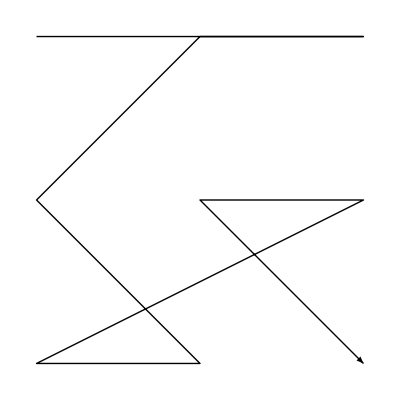
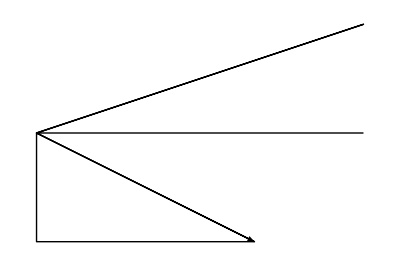
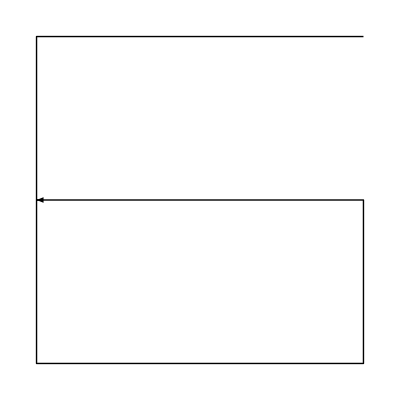
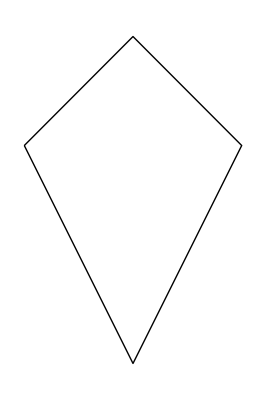
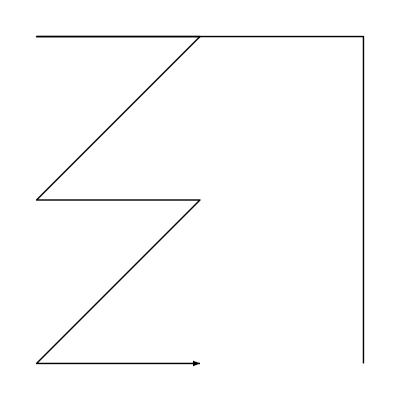
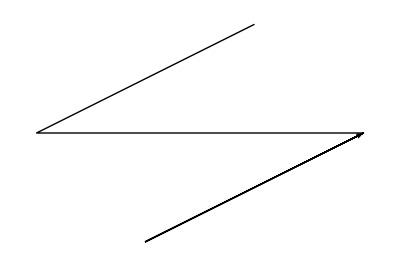
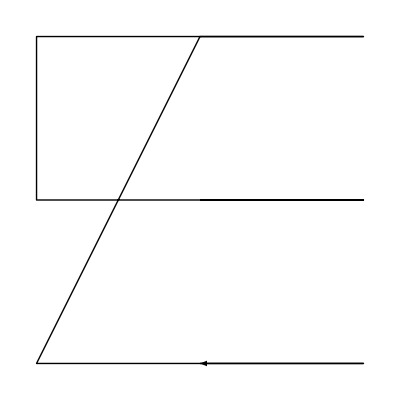
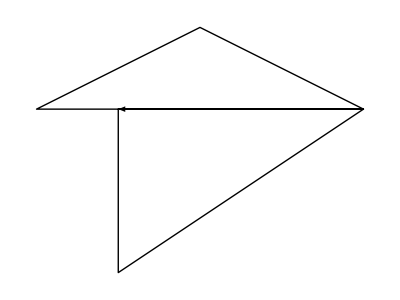
{(1 | 3 | 2
4 | 8 | 7
6 | 5 | 9),{-Graphics-,{{2,0},{-1,0},{-1,-1},{1,-1},{-1,0},{2,1},{-1,0},{1,-1}},-Graphics-}}
{(3 | 2 | 1
9 | 8 | 7
4 | 5 | 6),{-Graphics-,{{-1,0},{-1,0},{0,-2},{1,0},{1,0},{0,1},{-1,0},{-1,0}},-Graphics-}}
{(4 | 5 | 3
6 | 7 | 2
8 | 9 | 1),{-Graphics-,{{0,1},{0,1},{-2,0},{1,0},{-1,-1},{1,0},{-1,-1},{1,0}},-Graphics-}}
{(4 | 6 | 5
3 | 1 | 2
7 | 9 | 8),{-Graphics-,{{1,0},{-2,0},{0,1},{2,0},{-1,0},{-1,-2},{2,0},{-1,0}},-Graphics-}}
{(5 | 6 | 4
8 | 9 | 7
2 | 1 | 3),{-Graphics-,{{-1,0},{2,0},{0,2},{-2,0},{1,0},{1,-1},{-2,0},{1,0}},-Graphics-}}
{(6 | 4 | 5
3 | 7 | 8
9 | 1 | 2),{-Graphics-,{{1,0},{-2,1},{1,1},{1,0},{-2,0},{1,-1},{1,0},{-2,-1}},-Graphics-}}
{(7 | 8 | 9
3 | 2 | 1
4 | 5 | 6),{-Graphics-,{{-1,0},{-1,0},{0,-1},{1,0},{1,0},{-2,2},{1,0},{1,0}},-Graphics-}}
{(7 | 9 | 8
3 | 1 | 2
6 | 4 | 5),{-Graphics-,{{1,0},{-2,0},{1,-1},{1,0},{-2,0},{0,2},{2,0},{-1,0}},-Graphics-}}
{(8 | 9 | 1
2 | 3 | 7
5 | 6 | 4),{-Graphics-,{{-2,-1},{1,0},{1,-1},{-2,0},{1,0},{1,1},{-2,1},{1,0}},-Graphics-}}
{(8 | 9 | 7
5 | 4 | 6
2 | 1 | 3),{-Graphics-,{{-1,0},{2,0},{-1,1},{-1,0},{2,0},{0,1},{-2,0},{1,0}},-Graphics-}}
{(1 | 8 | 7
6 | 5 | 9
2 | 3 | 4),{-Graphics-,{{0,-2},{1,0},{1,0},{-1,1},{-1,0},{2,1},{-1,0},{1,-1}},-Graphics-}}
{(2 | 5 | 4
3 | 9 | 7
1 | 8 | 6),{-Graphics-,{{0,2},{0,-1},{2,1},{-1,0},{1,-2},{0,1},{-1,-1},{0,1}},-Graphics-}}
{(3 | 8 | 4
2 | 9 | 6
5 | 7 | 1),{-Graphics-,{{-2,1},{0,1},{2,0},{-2,-2},{2,1},{-1,-1},{0,2},{0,-1}},-Graphics-}}
{(3 | 9 | 7
5 | 8 | 2
4 | 6 | 1),{-Graphics-,{{0,1},{-2,1},{0,-2},{0,1},{1,-1},{1,2},{-1,-1},{0,1}},-Graphics-}}
{(4 | 1 | 6
8 | 3 | 5
7 | 2 | 9),{-Graphics-,{{0,-2},{0,1},{-1,1},{2,-1},{0,1},{-2,-2},{0,1},{2,-1}},-Graphics-}}
{(4 | 2 | 1
8 | 9 | 6
7 | 5 | 3),{-Graphics-,{{-1,0},{1,-2},{-2,2},{1,-2},{1,1},{-2,-1},{0,1},{1,0}},-Graphics-}}
{(4 | 5 | 6
3 | 7 | 9
8 | 2 | 1),{-Graphics-,{{-1,0},{-1,1},{0,1},{1,0},{1,0},{-1,-1},{-1,-1},{2,1}},-Graphics-}}
{(4 | 9 | 1
3 | 6 | 2
5 | 7 | 8),{-Graphics-,{{0,-1},{-2,0},{0,1},{0,-2},{1,1},{0,-1},{1,0},{-1,2}},-Graphics-}}
{(5 | 1 | 4
9 | 2 | 7
8 | 3 | 6),{-Graphics-,{{0,-1},{0,-1},{1,2},{-2,0},{2,-2},{0,1},{-2,-1},{0,1}},-Graphics-}}
{(5 | 2 | 7
4 | 3 | 9
8 | 1 | 6),{-Graphics-,{{0,2},{0,-1},{-1,0},{0,1},{2,-2},{0,2},{-2,-2},{2,1}},-Graphics-}}
{(6 | 3 | 2
8 | 5 | 7
9 | 4 | 1),{-Graphics-,{{0,2},{-1,0},{0,-2},{0,1},{-1,1},{2,-1},{-2,0},{0,-1}},-Graphics-}}
{(7 | 6 | 9
5 | 3 | 4
8 | 2 | 1),{-Graphics-,{{-1,0},{0,1},{1,0},{-2,0},{1,1},{-1,0},{0,-2},{2,2}},-Graphics-}}
{(7 | 9 | 2
8 | 5 | 3
4 | 6 | 1),{-Graphics-,{{0,2},{0,-1},{-2,-1},{1,1},{0,-1},{-1,2},{0,-1},{1,1}},-Graphics-}}
{(8 | 9 | 5
7 | 1 | 4
3 | 6 | 2),{-Graphics-,{{1,-1},{-2,0},{2,1},{0,1},{-1,-2},{-1,1},{0,1},{1,0}},-Graphics-}}

```mathematica
Map[GM[Last[#]]&,gg]//Column
```

```mathematica
{({{3, 9, 7}, {5, 8, 2}, {4, 6, 1}}),{-Graphics-,{{0,1},{-2,1},{0,-2},{0,1},{1,-1},{1,2},{-1,-1},{0,1}},-Graphics-}}
{({{4, 5, 3}, {6, 7, 2}, {8, 9, 1}}),{-Graphics-,{{0,1},{0,1},{-2,0},{1,0},{-1,-1},{1,0},{-1,-1},{1,0}},-Graphics-}}
```

```mathematica
Det[({{3, 9, 7}, {5, 8, 2}, {4, 6, 1}})]
Det[({{4, 5, 3}, {6, 7, 2}, {8, 9, 1}})]
```

1

0

```mathematica
ff[x_]:=FindPermutation[Flatten[{{4,9,2},{3,5,7},{8,1,6}}],Flatten[x]]
```

```mathematica
Map[ff[Last[#]]&,gg]
```

{Cycles[{{1,4,2,9,7,5,8}}],Cycles[{{1,7,5,8,3,2,4}}],Cycles[{{2,8,9,4,3,6,5}}],Cycles[{{2,8,5,3,6,7,9}}],Cycles[{{1,3,7,4,9,2,5}}],Cycles[{{1,2,7,6,5,3,9}}],Cycles[{{1,7,2,3,5,8,6}}],Cycles[{{1,8,5,9,7,3,6}}],Cycles[{{1,9,8,3,4,5,7}}],Cycles[{{1,5,4,9,6,3,7}}],Cycles[{{1,9,4,8},{2,6,3,7}}],Cycles[{{1,3},{2,5},{7,8}}],Cycles[{{1,3,4},{2,5,7},{6,8,9}}],Cycles[{{1,7,5,4},{3,6},{8,9}}],Cycles[{{2,9,3,8},{4,5,6,7}}],Cycles[{{2,5,8,3},{4,9,6,7}}],Cycles[{{2,6,5},{3,8,9}}],Cycles[{{3,6,8},{5,7,9}}],Cycles[{{1,3,5},{2,4,8}}],Cycles[{{1,4,5},{2,6,3}}],Cycles[{{1,8,9},{2,7,4}}],Cycles[{{1,6},{2,3,8,9},{4,5}}],Cycles[{{1,7,4,6},{8,9}}],Cycles[{{1,6,4,7},{3,9,8,5}}]}

```mathematica
pg=PermutationGroup[%]
```

PermutationGroup[{Cycles[{{1,4,2,9,7,5,8}}],Cycles[{{1,7,5,8,3,2,4}}],Cycles[{{2,8,9,4,3,6,5}}],Cycles[{{2,8,5,3,6,7,9}}],Cycles[{{1,3,7,4,9,2,5}}],Cycles[{{1,2,7,6,5,3,9}}],Cycles[{{1,7,2,3,5,8,6}}],Cycles[{{1,8,5,9,7,3,6}}],Cycles[{{1,9,8,3,4,5,7}}],Cycles[{{1,5,4,9,6,3,7}}],Cycles[{{1,9,4,8},{2,6,3,7}}],Cycles[{{1,3},{2,5},{7,8}}],Cycles[{{1,3,4},{2,5,7},{6,8,9}}],Cycles[{{1,7,5,4},{3,6},{8,9}}],Cycles[{{2,9,3,8},{4,5,6,7}}],Cycles[{{2,5,8,3},{4,9,6,7}}],Cycles[{{2,6,5},{3,8,9}}],Cycles[{{3,6,8},{5,7,9}}],Cycles[{{1,3,5},{2,4,8}}],Cycles[{{1,4,5},{2,6,3}}],Cycles[{{1,8,9},{2,7,4}}],Cycles[{{1,6},{2,3,8,9},{4,5}}],Cycles[{{1,7,4,6},{8,9}}],Cycles[{{1,6,4,7},{3,9,8,5}}]}]

```mathematica
GroupOrder[pg]
```

362880

```mathematica
CayleyGraph[pg]
```

```mathematica
Table[GroupOrbits[pg,{i}],{i,1,10000}]
```

```mathematica
Map[GroupOrder[PermutationGroup[#]]&,Subsets[Map[ff[Last[#]]&,gg],{1}]]
```

{7,7,7,7,7,7,7,7,7,7,4,2,3,4,4,4,3,3,3,3,3,4,4,4}

```mathematica
DeleteDuplicates[Map[GroupOrder[PermutationGroup[#]]&,Subsets[Map[ff[Last[#]]&,gg],{2}]]]
```

{1344,181440,20160,40320,5040,1512,168,362880,2520,504,1440,32,360,336,42,24,48,72,216,480,80,21,720,2160,192,576}

```mathematica
DeleteDuplicates[Map[GroupOrder[PermutationGroup[#]]&,Subsets[Map[ff[Last[#]]&,gg],{3}]]]
```

{181440,20160,40320,362880,1344,5040,2520,10080,480,168}

```mathematica
DeleteDuplicates[Map[GroupOrder[PermutationGroup[#]]&,Subsets[Map[ff[Last[#]]&,gg],{4}]]]
```

{181440,362880,20160,40320}

```mathematica
DeleteDuplicates[Map[GroupOrder[PermutationGroup[#]]&,Subsets[Map[ff[Last[#]]&,gg],{5}]]]
```

{181440,362880,40320,20160}

```mathematica
DeleteDuplicates[Map[GroupOrder[PermutationGroup[#]]&,Subsets[Map[ff[Last[#]]&,gg],{6}]]]
```

{181440,362880,40320,20160}